```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
(*BlockadeRadius->Sqrt[2]*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
RydDev[Gates][[All,1]]
```

-Graphics3D-

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAPDCG_(q1$_Integer,q2$_Integer),SWAPDCH_(q1$_Integer,q2$_Integer),InstaSWAP_(q1_,q2_),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$889958,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$889958[{p$,q$}],CZG_(p$_Integer,q$_Integer)/;blockadeCheck$889958[{p$,q$}],CZH_(p$_Integer,q$_Integer)/;blockadeCheck$889958[{p$,q$}],CCZ_(i$_,j$_,k$_)/;blockadeCheck$889958[{i$,j$}]/;blockadeCheck$889958[{j$,k$}]/;blockadeCheck$889958[{k$,i$}],C_c$_[Z_t$__]/;blockadeCheck$889958[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$889958[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$889958[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[CZG, 0,1]},RydDev,ReplaceAliases->True]]
```

{UNonNorm_(0,1)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7]}

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
```

```mathematica
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Pelegri CZ*)
MoveTime=500;
SU4GateGINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, Levine CZ*)
SU4GateHINSTA[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Pelegri CZ*)
SU4GateGDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCG], a[[1]],a[[2]]],Subscript[CZG, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, Levine CZ*)
SU4GateHDC[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCH], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Pelegri CZ*)
SU4GateGMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZG,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, Movement Procedure, Levine CZ*)
SU4GateHMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZH,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*SU4Gate[data[[400;;1000]][[112]],0,1]*)
```

```mathematica
(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

```mathematica
(*Generate a layer of gates for building a QV circuit*)
QVLayerGA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateGINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateGDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCG, RQs[[n+1]],3]},SU4GateGDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCG, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerGMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateGMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];

QVLayerHA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateHINSTA[DataSet[[n+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateHDC[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCH, RQs[[n+1]],3]},SU4GateHDC[DataSet[[n+i]],RQs[[n]],3]],{Subscript[SWAPDCH, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerHMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateHMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];
```

```mathematica
ExtractCircuit[InsertCircuitNoise[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},RydDev]]
```

{Deph_0[0.000167757],Deph_1[0.000167757],Deph_2[0.000167757],Deph_3[0.000167757],Deph_4[0.000167757],Deph_5[0.000167757],Deph_6[0.000167757],Deph_7[0.000167757],Deph_8[0.000167757],Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}

```mathematica
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Table[RQS=NRandQbits[NQ];Layer=Which[StringContainsQ[ConnectivityRule,"GA2A"],QVLayerGA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GSWAP"],QVLayerGSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"GMove"],QVLayerGMove[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HA2A"],QVLayerHA2A[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HSWAP"],QVLayerHSWAP[DataSet,NQ,RQS,i],StringContainsQ[ConnectivityRule,"HMove"],QVLayerHMove[DataSet,NQ,RQS,i]];
(*Print["# Qubits, ",NQ," # Gates per Layer, ",Length[Layer]]*);Flatten[Layer],{i,0,NQ-1,1}]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
Which[StringContainsQ[ConnectivityRule,"HMove"],PoutcomesNoisy=PoutcomesNoisy/(1-MeanRenormHMove[[NQ-1]]),StringContainsQ[ConnectivityRule,"GMove"],PoutcomesNoisy=PoutcomesNoisy/(1-MeanRenormGMove[[NQ-1]])];
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
Total[HeavyOutputs],{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
MHOP=Mean[HOP];
σ=StandardDeviation[HOP]/Sqrt[NReps-1];;
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
Print[{"Layer",NQ,VQ}];
{NQ,MHOP,2σ}
,{NQ,2,MaxNQ,1}];

(*GA2AQV=QVCalc[data,9,200,"GA2A"]
GSWAPQV=QVCalc[data,9,200,"GSWAP"]*)
(*HA2AQV=QVCalc[data,9,200,"HA2A"]
HSWAPQV=QVCalc[data,9,200,"HSWAP"]*)

GMoveQV=QVCalc[data,9,200,"GMove"]
HMoveQV=QVCalc[data,9,200,"HMove"]
DestroyAllQuregs[];
```

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{{2,0.786021,0.0139088},{3,0.847087,0.0123368},{4,0.831373,0.00726228},{5,0.850482,0.00577239},{6,0.839353,0.00380182},{7,0.841118,0.00336454},{8,0.828258,0.00189946},{9,0.825211,0.0014891}}

```mathematica
GMoveQV
```

{{2,0.797108,0.0128986},{3,0.851692,0.0124526},{4,0.837986,0.00759597},{5,0.855545,0.00517676},{6,0.843309,0.00339957},{7,0.846971,0.00304184},{8,0.832896,0.00208175},{9,0.831794,0.00152376}}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,0}

{Layer,8,0}

{Layer,9,0}

```mathematica
MeanRenormHMove=Table[Mean[RenormFactorHMove[[i]]],{i,1,Length[RenormFactorHA2A]}]
MeanRenormGSWAP=Table[Mean[RenormFactorGSWAP[[i]]],{i,1,Length[RenormFactorGSWAP]}]
```

{0.0665524,0.0692619,0.0825512,0.0876574,0.108157,0.115759,0.143205,0.152819,Mean[{}]}

```mathematica
?QuEST`Gates
```

Missing[UnknownSymbol,QuEST`Gates]

```mathematica
CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{Subscript[CZH, 0,1]},RydDev,ReplaceAliases->True]]]
```

CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{CZH_(0,1)},RydDev,ReplaceAliases→True]]]

```mathematica
GA2AQVUnNorm={{2,0.7405816455278738,0.012891402234974744},{3,0.7763156324179025,0.010735056357840861},{4,0.7496847408842636,0.006620655826557423},{5,0.7626388038383476,0.0051446438862961},{6,0.7277371459047844,0.002728320896540523},{7,0.7198160946731358,0.002559978776835931},{8,0.6735455321130638,0.0014137201886522943},{9,0.6608622975551284,0.0011299567629418342}}
```

{{2,0.740582,0.0128914},{3,0.776316,0.0107351},{4,0.749685,0.00662066},{5,0.762639,0.00514464},{6,0.727737,0.00272832},{7,0.719816,0.00255998},{8,0.673546,0.00141372},{9,0.660862,0.00112996}}

```mathematica
GSWAPQVUnNorm={{2,0.734151602191516,0.012203688063819421},{3,0.7796258146926748,0.0114042182741467},{4,0.7584907533431214,0.0066033072782086056},{5,0.7467017004789538,0.005105813066262238},{6,0.6881346044369444,0.003464302233772094},{7,0.6614145781024228,0.0028625009400299085},{8,0.5888492972994888,0.0024423096373259057},{9,0.5588482658031424,0.002553979984975081}}
GMoveQVUnNorm={{2,0.7316097045776994,0.012453361680376711},{3,0.7912486808307285,0.011152390054086006},{4,0.7565998978239634,0.006552142857848809},{5,0.7587936023582366,0.004799933512465381},{6,0.7248659575145965,0.0031892410072394428},{7,0.7153719352535137,0.0024610562966784896},{8,0.665925680366202,0.0015435275606227416},{9,0.6507702335994054,0.0011162694769176094}}
```

{{2,0.734152,0.0122037},{3,0.779626,0.0114042},{4,0.758491,0.00660331},{5,0.746702,0.00510581},{6,0.688135,0.0034643},{7,0.661415,0.0028625},{8,0.588849,0.00244231},{9,0.558848,0.00255398}}

{{2,0.73161,0.0124534},{3,0.791249,0.0111524},{4,0.7566,0.00655214},{5,0.758794,0.00479993},{6,0.724866,0.00318924},{7,0.715372,0.00246106},{8,0.665926,0.00154353},{9,0.65077,0.00111627}}

```mathematica
HA2AQVUnNorm={{2,0.7401509835586911,0.011720393627843191},{3,0.7861195373963302,0.010947768305616145},{4,0.7735466762741807,0.006139049269876257},{5,0.7755597101341623,0.004957302000898714},{6,0.7540040405551361,0.0032992294402544075},{7,0.7517134081713516,0.0025793579054604354},{8,0.7184799655663686,0.0017272340009129104},{9,0.7097760794016982,0.001339681908122264}}
```

{{2,0.740151,0.0117204},{3,0.78612,0.0109478},{4,0.773547,0.00613905},{5,0.77556,0.0049573},{6,0.754004,0.00329923},{7,0.751713,0.00257936},{8,0.71848,0.00172723},{9,0.709776,0.00133968}}

```mathematica
HSWAPQVUnNorm={{2,0.7435531945073748,0.011901007879567028},{3,0.7940027426701181,0.010321949703200325},{4,0.7659901802837689,0.007085147237230059},{5,0.7647139244545597,0.005664124187713016},{6,0.7273886156772132,0.003525305196753448},{7,0.712418857446769,0.0028805781172344053},{8,0.6550670104692926,0.002483069085888343},{9,0.6322294208564452,0.0023273933185776912}}
```

{{2,0.743553,0.011901},{3,0.794003,0.0103219},{4,0.76599,0.00708515},{5,0.764714,0.00566412},{6,0.727389,0.00352531},{7,0.712419,0.00288058},{8,0.655067,0.00248307},{9,0.632229,0.00232739}}

```mathematica
HMoveQVUnNorm={{2,0.7359837396494435,0.012665090894074575},{3,0.7904297004887582,0.010958052382184134},{4,0.7677433251358556,0.0064855437900339435},{5,0.7800894334429009,0.005242273136270247},{6,0.7509344297889435,0.00316174524209156},{7,0.743504677658759,0.002576245716119806},{8,0.7094708481092695,0.001627629659813381},{9,0.699616183100201,0.0012965356275318977}}
```

{{2,0.735984,0.0126651},{3,0.79043,0.0109581},{4,0.767743,0.00648554},{5,0.780089,0.00524227},{6,0.750934,0.00316175},{7,0.743505,0.00257625},{8,0.709471,0.00162763},{9,0.699616,0.00129654}}

```mathematica
MeanRenormHA2A={0.0665402220585088,0.06936915034994637,0.08246500313651679,0.08761588246300792,0.10826942876131372,0.11587803153320925,0.14314265212040853,0.15274980616844716}
```

{0.0665402,0.0693692,0.082465,0.0876159,0.108269,0.115878,0.143143,0.15275}

```mathematica
MeanRenormHSWAP={0.06651223359498336,0.06933340641705779,0.08250450816446736,0.09732735475716929,0.1327290665614612,0.15529831976987418,0.20326674227961392,0.2262761074503026}
```

{0.0665122,0.0693334,0.0825045,0.0973274,0.132729,0.155298,0.203267,0.226276}

```mathematica
MeanRenormHMove={0.06655241346304827, 0.06926191675755718,0.08255116333487107,0.0876574148000778,0.10815734991256716,0.11575895425630245,0.14320458424230437,0.15281919753058623}
```

{0.0665524,0.0692619,0.0825512,0.0876574,0.108157,0.115759,0.143205,0.152819}

```mathematica
MeanRenormGA2A={0.07074940104421311,0.0755396303625562,0.09888697829524155,0.10773031675463329,0.14362599160166237,0.15670331182186956,0.202718259758029,0.21866533363205387}
MeanRenormGSWAP={0.07072197687583025,0.07560784800815645,0.09885574096018666,0.125646199165414,0.1835367688844255,0.220735713103119,0.29815794264489387,0.3334822180218006}
MeanRenormGMove={0.0707452085914006,0.07567024425526565,0.09854171621276976,0.10788256103612998,0.14333651197132707,0.1562577981098641,0.20274888369740773,0.21864817610273504}
```

{0.0707494,0.0755396,0.098887,0.10773,0.143626,0.156703,0.202718,0.218665}

{0.070722,0.0756078,0.0988557,0.125646,0.183537,0.220736,0.298158,0.333482}

{0.0707452,0.0756702,0.0985417,0.107883,0.143337,0.156258,0.202749,0.218648}

```mathematica
GA2AQVRenorm={{2,0.79079121496538±0.013524801785153353},{3,0.8489587791370138±0.011987730709441608},{4,0.8384361547827764±0.0070229755998004635},{5,0.8566745449343114±0.005393198979184408},{6,0.8500726204105155±0.003827795673738825},{7,0.8542196981782405±0.002813378105357417},{8,0.8441067931395366±0.001997463066941062},{9,0.8454409614573727±0.0013928806307027552}}
GSWAPQVRenorm={{2,0.7922549774371156±0.0141165918715427},{3,0.8472778724587833±0.01245063626803773},{4,0.8311756513202974±0.007313345567025717},{5,0.8596835903542691±0.005757862880054895},{6,0.8460001982372652±0.0043378621102428665},{7,0.8499306186085411±0.0038228215163547802},{8,0.8374276975058441±0.003750293688273244},{9,0.8354296432289274±0.0034930655432672216}}
GMoveQVRenorm={{2,0.797107593010428±0.012898644132759601},{3,0.851691990239746±0.012452588177536217},{4,0.8379864267360843±0.0075959651136756805},{5,0.855544552071303±0.005176758865118236},{6,0.8433089449367895±0.0033995744773940182},{7,0.8469706618475393±0.003041835600156929},{8,0.8328961760327086±0.00208175486602617},{9,0.8317938000779861±0.001523759850160512}}
```

{{2,0.790791±0.0135248},{3,0.848959±0.0119877},{4,0.838436±0.00702298},{5,0.856675±0.0053932},{6,0.850073±0.0038278},{7,0.85422±0.00281338},{8,0.844107±0.00199746},{9,0.845441±0.00139288}}

{{2,0.792255±0.0141166},{3,0.847278±0.0124506},{4,0.831176±0.00731335},{5,0.859684±0.00575786},{6,0.846±0.00433786},{7,0.849931±0.00382282},{8,0.837428±0.00375029},{9,0.83543±0.00349307}}

{{2,0.797108±0.0128986},{3,0.851692±0.0124526},{4,0.837986±0.00759597},{5,0.855545±0.00517676},{6,0.843309±0.00339957},{7,0.846971±0.00304184},{8,0.832896±0.00208175},{9,0.831794±0.00152376}}

```mathematica
HA2AQVRenorm={{2,0.7895406850254238±0.013737026566374662},{3,0.8495997028586166±0.012012553913266884},{4,0.8348508349866097±0.0070277610166078665},{5,0.8555165135009669±0.005663812268499948},{6,0.8445639541713855±0.00408156530877206},{7,0.8511686618078806±0.0029856417429019286},{8,0.8379757405830542±0.002150526821011032},{9,0.8378251734924934±0.001512796740746905}}

HSWAPQVRenorm={{2,0.7902552437379439±0.01384407174922472},{3,0.8486659579417659±0.012215787267853688},{4,0.8382793607760826±0.006704505388549647},{5,0.846127939207912±0.005854623275864581},{6,0.8464296908209206±0.004054319642496805},{7,0.8390873816070714±0.0037142443321610094},{8,0.8260365898542622±0.003011805797972457},{9,0.8166398081285762±0.003156891926526585}}
HMoveQVRenorm={{2,0.7860211890945226±0.013908767589961903},{3,0.8470873110638029±0.012336846799916618},{4,0.8313732663443375±0.007262278323814587},{5,0.85048199725319±0.0057723893095098285},{6,0.8393529806487345±0.00380181720776509},{7,0.8411178138896994±0.0033645361481727297},{8,0.8282576131424173±0.0018994634645571667},{9,0.8252110631170132±0.0014891011166331073}}
```

{{2,0.789541±0.013737},{3,0.8496±0.0120126},{4,0.834851±0.00702776},{5,0.855517±0.00566381},{6,0.844564±0.00408157},{7,0.851169±0.00298564},{8,0.837976±0.00215053},{9,0.837825±0.0015128}}

{{2,0.790255±0.0138441},{3,0.848666±0.0122158},{4,0.838279±0.00670451},{5,0.846128±0.00585462},{6,0.84643±0.00405432},{7,0.839087±0.00371424},{8,0.826037±0.00301181},{9,0.81664±0.00315689}}

{{2,0.786021±0.0139088},{3,0.847087±0.0123368},{4,0.831373±0.00726228},{5,0.850482±0.00577239},{6,0.839353±0.00380182},{7,0.841118±0.00336454},{8,0.828258±0.00189946},{9,0.825211±0.0014891}}

```mathematica
RenormFactorGSWAP
```

{{},{},{},{},{},{},{},{}}

```mathematica
CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{Subscript[CZG, 0,1]},RydDev,ReplaceAliases->True]]]
```

CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{CZG_(0,1)},RydDev,ReplaceAliases→True]]]

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
```

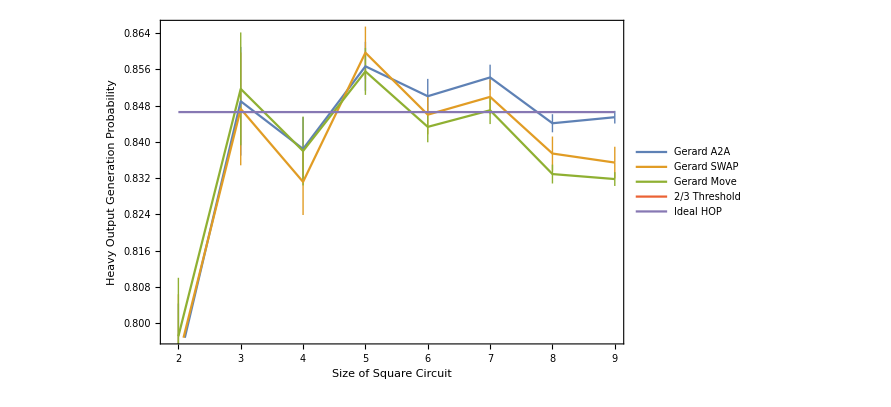

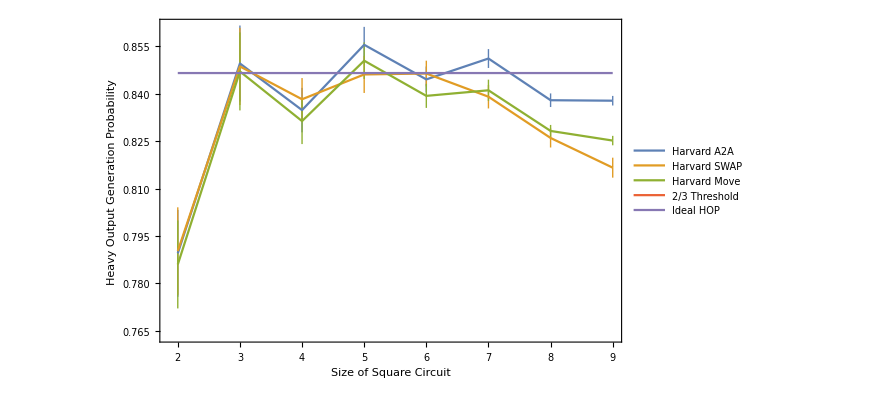

```mathematica
ListLinePlot[{GA2AQVRenorm,GSWAPQVRenorm,GMoveQVRenorm,Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Gerard A2A","Gerard SWAP","Gerard Move","2/3 Threshold","Ideal HOP"}]
ListLinePlot[{HA2AQVRenorm,HSWAPQVRenorm,HMoveQVRenorm,Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Harvard A2A","Harvard SWAP","Harvard Move","2/3 Threshold","Ideal HOP"}]
```

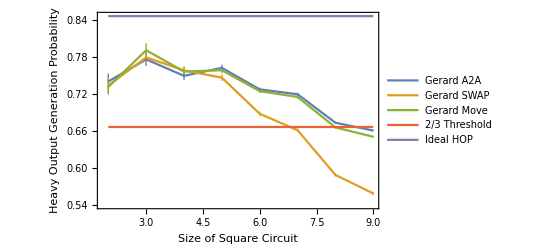

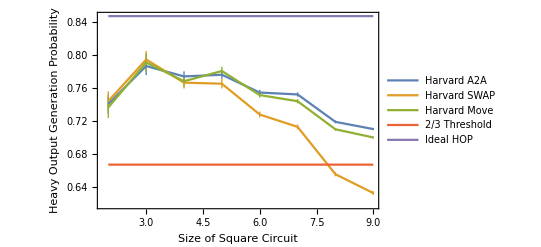

```mathematica
ErrorBar[DataSet_]:=Table[{DataSet[[i,1]],DataSet[[i,2]]±DataSet[[i,3]]},{i,1,Length[DataSet]}]
ListLinePlot[{ErrorBar[GA2AQVUnNorm],ErrorBar[GSWAPQVUnNorm],ErrorBar[GMoveQVUnNorm],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Gerard A2A","Gerard SWAP","Gerard Move","2/3 Threshold","Ideal HOP"}]
ListLinePlot[{ErrorBar[HA2AQVUnNorm],ErrorBar[HSWAPQVUnNorm],ErrorBar[HMoveQVUnNorm],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Harvard A2A","Harvard SWAP","Harvard Move","2/3 Threshold","Ideal HOP"}]
```

```mathematica
PlusMinus[1]
```

±1